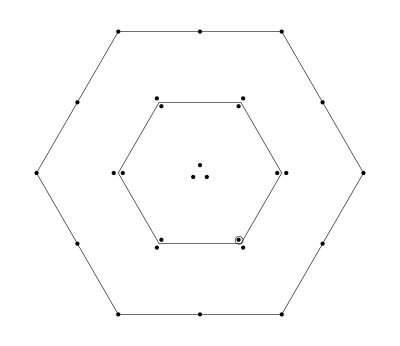

Y=-1.5,  I_3=0.5

(us+su)(ūd̄+d̄ū)+2ss(s̄d̄+d̄s̄)-3(sd+ds)d̄d̄

```mathematica
(*-------------------------------*)
```

The current J:

3 ((d̄)_a γ^μ C((d̄)_b)^T-(d̄)_b γ^μ C((d̄)_a)^T) (d_a^T C γ^μ s_b)+3 ((d̄)_a γ^μ C((d̄)_b)^T-(d̄)_b γ^μ C((d̄)_a)^T) (s_a^T C γ^μ d_b)+2 (s_a^T C γ^μ s_b) ((d̄)_b γ^μ C((s̄)_a)^T-(s̄)_a γ^μ C((d̄)_b)^T)+2 (s_a^T C γ^μ s_b) ((s̄)_b γ^μ C((d̄)_a)^T-(d̄)_a γ^μ C((s̄)_b)^T)+(s_a^T C γ^μ u_b) ((d̄)_b γ^μ C((ū)_a)^T-(ū)_a γ^μ C((d̄)_b)^T)+(u_a^T C γ^μ s_b) ((d̄)_b γ^μ C((ū)_a)^T-(ū)_a γ^μ C((d̄)_b)^T)+(s_a^T C γ^μ u_b) ((ū)_b γ^μ C((d̄)_a)^T-(d̄)_a γ^μ C((ū)_b)^T)+(u_a^T C γ^μ s_b) ((ū)_b γ^μ C((d̄)_a)^T-(d̄)_a γ^μ C((ū)_b)^T)

the Fierz rearranged J (to naively get the decay partten)

```mathematica
-6 (d̄(γ^μ).(γ̄)^5 d d̄(γ^μ).(γ̄)^5 s)+4 (d̄(γ^μ).(γ̄)^5 s s̄(γ^μ).(γ̄)^5 s)+6 (d̄ γ^μ d d̄ γ^μ s)-4 (d̄ γ^μ s s̄ γ^μ s)+4 (d̄(γ̄)^5 s) (2 (s̄(γ̄)^5 s)-3 (d̄(γ̄)^5 d))+2 (d̄(γ^μ).(γ̄)^5 s ū(γ^μ).(γ̄)^5 u)+2 (d̄(γ^μ).(γ̄)^5 u ū(γ^μ).(γ̄)^5 s)-2 (d̄ γ^μ s ū γ^μ u)-2 (d̄ γ^μ u ū γ^μ s)+4 (d̄(γ̄)^5 s ū(γ̄)^5 u)+4 (d̄(γ̄)^5 u ū(γ̄)^5 s)-4 (d̄ 1s ū 1u)-4 (d̄ 1u ū 1s)+4 (d̄ 1s) (3 (d̄ 1d)-2 (s̄ 1s))
```

Π(q^2)=
-(log(-q^2/μ^2) q^8)/(128 π^6)-(5 ⟨ GG ⟩ log(-q^2/μ^2) q^4)/(32 π^5)-(⟨ d̄ d⟩ log(-q^2/μ^2) (15 m_d-13 m_s-2 m_u) q^4)/(12 π^4)+(⟨ ū u⟩ log(-q^2/μ^2) (m_d+m_s-2 m_u) q^4)/(6 π^4)+(⟨ s̄ s⟩ log(-q^2/μ^2) (13 m_d-15 m_s+2 m_u) q^4)/(12 π^4)-(30 ⟨ d̄ d⟩^2 log(-q^2/μ^2) q^2)/π^2-(40 ⟨ s̄ s⟩^2 log(-q^2/μ^2) q^2)/(3 π^2)-(8 ⟨ ū u⟩^2 log(-q^2/μ^2) q^2)/(3 π^2)+(125 ⟨G^3⟩ log(-q^2/μ^2) q^2)/(576 π^6)+(70 ⟨ d̄ d⟩ ⟨ s̄ s⟩ log(-q^2/μ^2) q^2)/(3 π^2)+(44 ⟨ d̄ d⟩ ⟨ ū u⟩ log(-q^2/μ^2) q^2)/(3 π^2)-(12 ⟨ s̄ s⟩ ⟨ ū u⟩ log(-q^2/μ^2) q^2)/π^2+(3 ⟨ d̄ d⟩ ⟨ d̄ Gd⟩ log(-q^2/μ^2))/π^2+(13 ⟨ s̄ s⟩ ⟨ d̄ Gd⟩ log(-q^2/μ^2))/(6 π^2)+(⟨ ū u⟩ ⟨ d̄ Gd⟩ log(-q^2/μ^2))/(3 π^2)+(13 ⟨ d̄ d⟩ ⟨ s̄ Gs⟩ log(-q^2/μ^2))/(6 π^2)+(4 ⟨ s̄ s⟩ ⟨ s̄ Gs⟩ log(-q^2/μ^2))/(3 π^2)+(⟨ ū u⟩ ⟨ s̄ Gs⟩ log(-q^2/μ^2))/(3 π^2)+(⟨ d̄ d⟩ ⟨ ū Gu⟩ log(-q^2/μ^2))/(3 π^2)+(⟨ s̄ s⟩ ⟨ ū Gu⟩ log(-q^2/μ^2))/(3 π^2)-(7 ⟨ GG ⟩ ⟨ d̄ d⟩^2)/(π q^2)-(28 ⟨ GG ⟩ ⟨ s̄ s⟩^2)/(9 π q^2)-(8 ⟨ GG ⟩ ⟨ ū u⟩^2)/(9 π q^2)-(33 ⟨ d̄ Gd⟩^2)/(64 π^2 q^2)-(11 ⟨ s̄ Gs⟩^2)/(48 π^2 q^2)+(109 ⟨ GG ⟩ ⟨ d̄ d⟩ ⟨ s̄ s⟩)/(9 π q^2)+(50 ⟨ GG ⟩ ⟨ d̄ d⟩ ⟨ ū u⟩)/(9 π q^2)-(10 ⟨ GG ⟩ ⟨ s̄ s⟩ ⟨ ū u⟩)/(3 π q^2)-(143 ⟨ d̄ Gd⟩ ⟨ s̄ Gs⟩)/(192 π^2 q^2)-(11 ⟨ d̄ Gd⟩ ⟨ ū Gu⟩)/(96 π^2 q^2)-(11 ⟨ s̄ Gs⟩ ⟨ ū Gu⟩)/(96 π^2 q^2)-(8 ⟨ d̄ d⟩^2 ⟨ s̄ s⟩ (-22 m_d-17 m_s))/(3 q^2)-(128 ⟨ s̄ s⟩^2 ⟨ ū u⟩ (2 m_d+m_s))/(9 q^2)+(64 ⟨ d̄ d⟩^2 ⟨ ū u⟩ (m_d+2 m_s))/(3 q^2)-(8 ⟨ d̄ d⟩^3 (5 m_d+4 m_s))/q^2-(32 ⟨ s̄ s⟩^3 (4 m_d+5 m_s))/(9 q^2)+(32 ⟨ d̄ d⟩ ⟨ s̄ s⟩^2 (19 m_d+14 m_s))/(9 q^2)-(16 ⟨ d̄ d⟩ ⟨ ū u⟩^2 (2 m_d+m_u))/(9 q^2)-(16 ⟨ s̄ s⟩ ⟨ ū u⟩^2 (2 m_s+m_u))/(9 q^2)+(16 ⟨ d̄ d⟩ ⟨ s̄ s⟩ ⟨ ū u⟩ (15 m_d-5 m_s+8 m_u))/(9 q^2)

```mathematica
(*-------------------------------*)
```

ℳ^0(s_0) for η_6=η_8=η_10=1

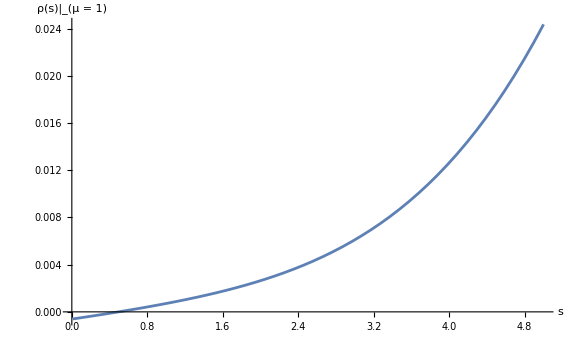
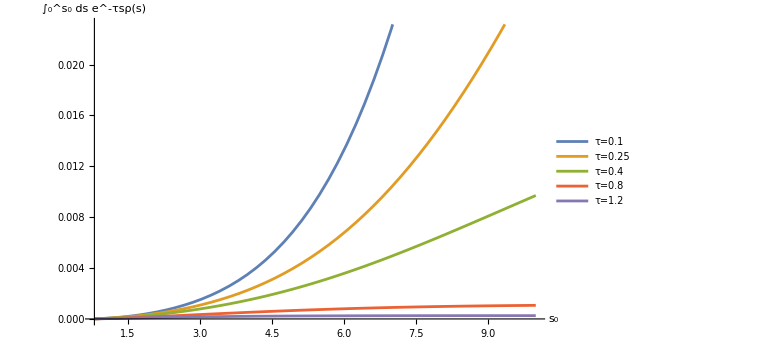

```mathematica
(*-------------------------------*)
```

(∫_0^s_0 dsC^i (s) ⟨𝒪_i⟩)/(∫_0^s_0 dsC^0 (s)) for η_6=η_8=η_10=1

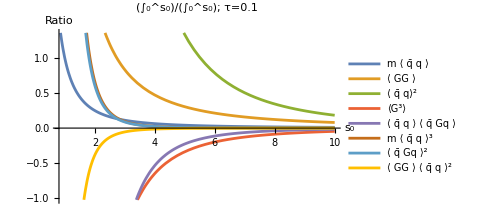
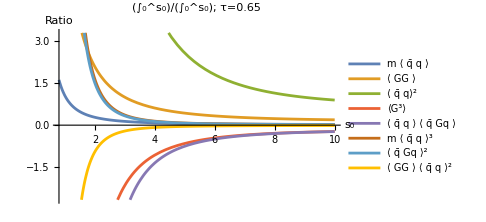
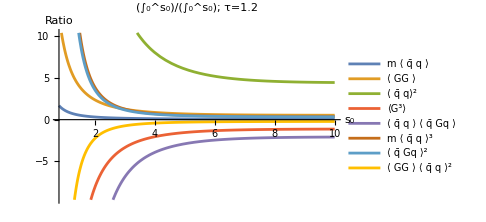

```mathematica
(*-------------------------------*)
```

ℛ^0 for η_6=η_8=η_10=1

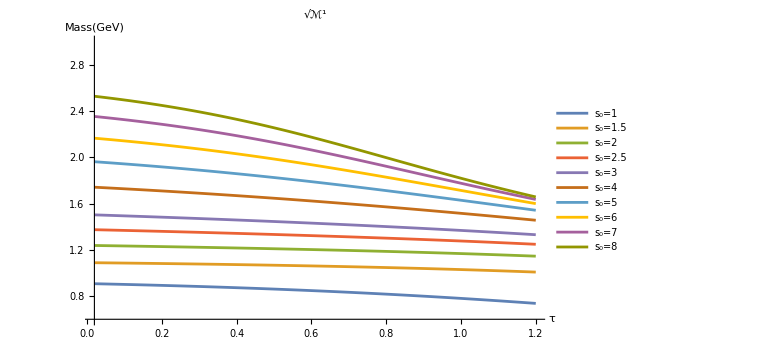
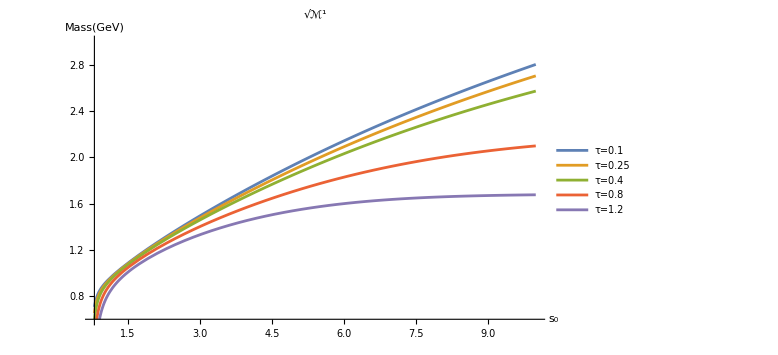

```mathematica
(*-------------------------------*)
```

ℛ^1 for η_6=η_8=η_10=1

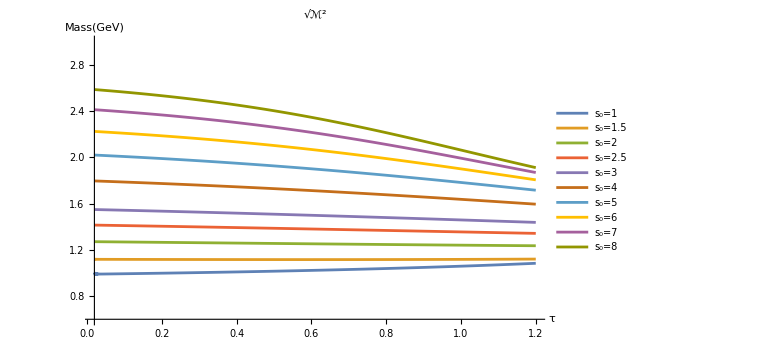
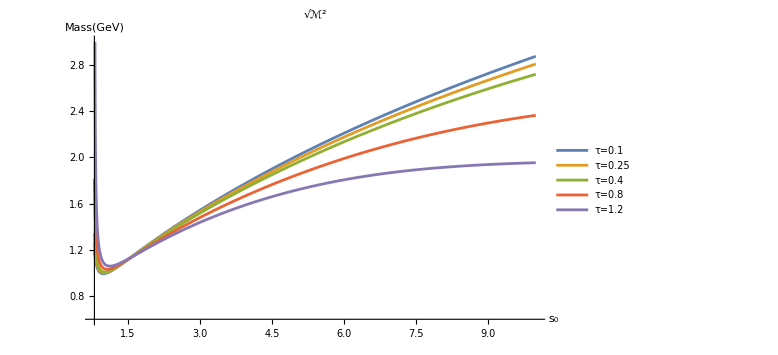

```mathematica
(*-------------------------------*)
```

ℳ^0(s_0) for η_6=3, η_8=5, η_10=5

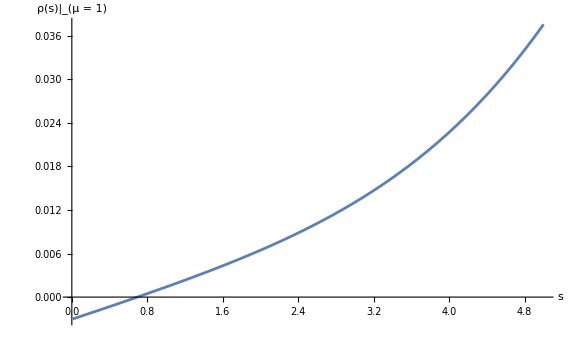
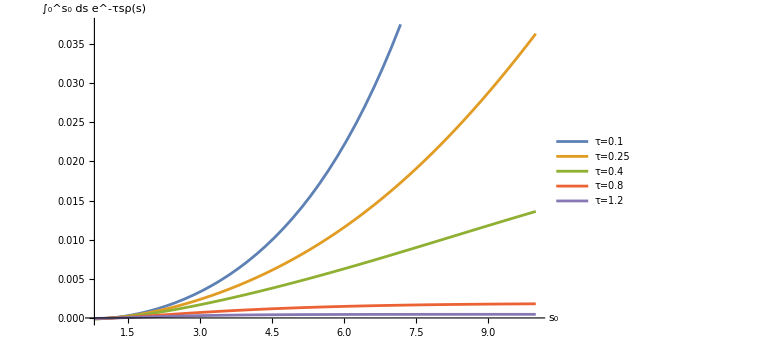

```mathematica
(*-------------------------------*)
```

(∫_0^s_0 dsC^i (s) ⟨𝒪_i⟩)/(∫_0^s_0 dsC^0 (s)) for η_6=3, η_8=5, η_10=5

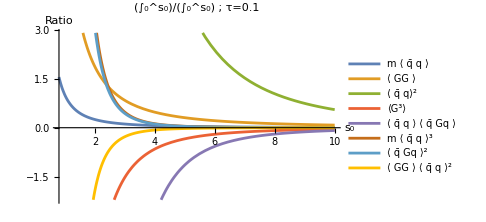
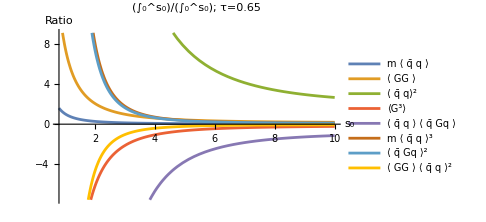
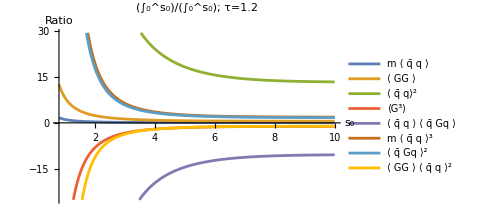

```mathematica
(*-------------------------------*)
```

ℛ^0 for η_6=3, η_8=5, η_10=5

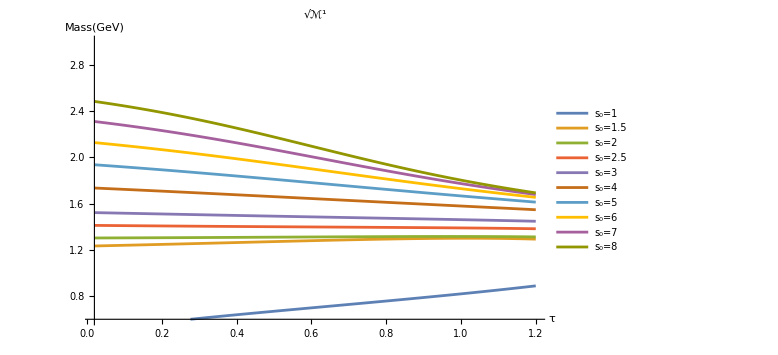
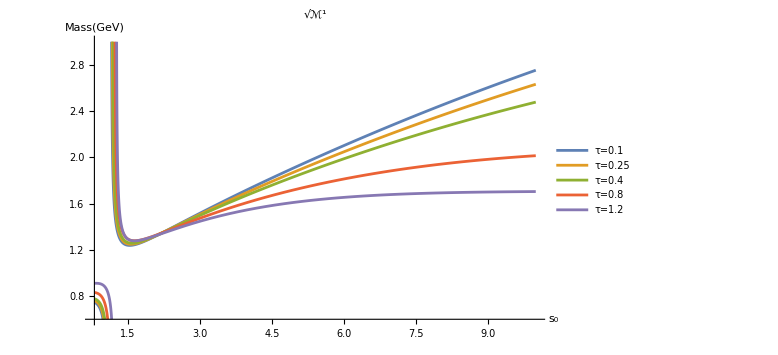

```mathematica
(*-------------------------------*)
```

ℛ^1 for η_6=3, η_8=5, η_10=5